## 1

```mathematica
Clear["Global`*"];
dim=3/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
Hmuti[ϕ1_,ϕ2_,ϕ3_]:=({{0, (√3)/2 ⅇ^(-ⅈ ϕ1), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ1), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}});
Iplus5half2=Ix3half2+I*Iy3half2;
Iminus5half2=Ix3half2-I*Iy3half2;
UHmuti[ϕ1_,ϕ2_,ϕ3_,t_]:=N[MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3]*t] ]
IniPhi={{1},{0},{0},{0}};

(*StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi*)

StateθϕInitial[θ_,ϕ_]:={{Cos[θ/2]^3},{1/4 √3 ⅇ^(ⅈ ϕ) Csc[θ/2] Sin[θ]^2},{1/2 √3 ⅇ^(2 ⅈ ϕ) Sin[θ/2] Sin[θ]},{ⅇ^(3 ⅈ ϕ) Sin[θ/2]^3}}

StateEvo[ϕ1_,ϕ2_,ϕ3_,t_,θ_,ϕ_]:=N[UHmuti[ϕ1,ϕ2,ϕ3,t].StateθϕInitial[θ,ϕ]]
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
Chop[N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]]
]
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
If[Chop[N[First[Flatten[yVal]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],Chop[N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]]
]

In1[state_]:=Chop[N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]]
In2[state_]:=Chop[N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]]
In1n2plusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]]
In1n2minusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]]
In1n2n2n1[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]]
ξSqure[state_]:=Chop[1*N[First[Flatten[  (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )^1/((ConjugateTranspose[state].Ix3half2.state)^2+(ConjugateTranspose[state].Iy3half2.state)^2+(ConjugateTranspose[state].Iz3half2.state)^2)]]]]
ξSqure2[state_]:=Chop[N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]],10^-8]



(*ξSqure[state_]:=Chop[N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]],10^-8]
*)
```

```mathematica
ξSqure[StateEvo[1,1,1,1,1,1]]
```

0.666667

```mathematica
phi1=Pi/2;
phi2=Pi/2;

ϕ1gra[ϕ1_,ϕ2_,ϕ3_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1-10^-8,ϕ2,ϕ3,t,phi1,phi2]]]])/10^-8
ϕ2gra[ϕ1_,ϕ2_,ϕ3_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2-10^-8,ϕ3,t,phi1,phi2]]]])/10^-8
ϕ3gra[ϕ1_,ϕ2_,ϕ3_,t_]:=(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3-10^-8,t,phi1,phi2]]]])/10^-8

ϕ1graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1-10^-8,ϕ2,ϕ3,t].state]]])/10^-8
ϕ2graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2-10^-8,ϕ3,t].state]]])/10^-8
ϕ3graState[ϕ1_,ϕ2_,ϕ3_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3-10^-8,t].state]]])/10^-8
```

```mathematica
durationnumber=1;
avenumber=20;
SqueezeTableduration=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
SqueezeTableduration2=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
phiMinTableduration=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
phiMinTableduration2=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber}];
Do[
Do[
If[Divisible[k,5],Print["durationnumber:",k,"  avenumber:",m]];
totT=0.4;
(*
totT=0.534/1;

totT=Pi/2*k/durationnumber;*)
itenumber=200;
ϕTable=Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}];

SqueezeTable=Table[0,{i,1,itenumber}];

SqueezeTable[[1]]=ξSqure[Chop[N[StateEvo[ϕTable[[1,1]],ϕTable[[1,2]],ϕTable[[1,3]],totT,phi1,phi2]]]];
Do[ 
ϕTable[[i,1]]=ϕTable[[i-1,1]]-0.4*ϕ1gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],totT];
ϕTable[[i,2]]=ϕTable[[i-1,2]]-0.4*ϕ2gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],totT];
ϕTable[[i,3]]=ϕTable[[i-1,3]]-0.4*ϕ3gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],totT];

SqueezeTable[[i]]=ξSqure[Chop[N[StateEvo[ϕTable[[i,1]],ϕTable[[i,2]],ϕTable[[i,3]],totT,phi1,phi2]]]];

(*If[Divisible[i,100],Print[N[i/itenumber]]];*)
,{i,2,itenumber}];

SqueezeTableduration[[k,m]]=Min[SqueezeTable];
phiMinTableduration[[k,m]]=ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]][[1]]]];



ExtraPiece=1;
ϕTableExtraPiece=Table[Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}],{j,1,ExtraPiece}];
StateExtraPiece=Table[0,{j,1,ExtraPiece+1}]; 
StateExtraPiece[[1]]=UHmuti[Last[ϕTable][[1]],Last[ϕTable][[2]],Last[ϕTable][[3]],totT].StateθϕInitial[phi1,phi2];
SqueezeTableExtraPiece=Table[Table[0,{i,1,itenumber}],{j,1,ExtraPiece}];
SqueezeTableExtraPiece[[1,1]]=ξSqure[StateExtraPiece[[1]]];
Do[

Do[ 
(*If[Divisible[i,100],Print["iter:",i,"  avenumber:",m]];*)
ϕTableExtraPiece[[j,i,1]]=ϕTableExtraPiece[[j,i-1,1]]-0.3*ϕ1graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,2]]=ϕTableExtraPiece[[j,i-1,2]]-0.3*ϕ2graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],totT,StateExtraPiece[[j]]];
ϕTableExtraPiece[[j,i,3]]=ϕTableExtraPiece[[j,i-1,3]]-0.3*ϕ3graState[ϕTableExtraPiece[[j,i-1,1]],ϕTableExtraPiece[[j,i-1,2]],ϕTableExtraPiece[[j,i-1,3]],totT,StateExtraPiece[[j]]];

SqueezeTableExtraPiece[[j,i]]=ξSqure[Chop[N[UHmuti[ϕTableExtraPiece[[j,i,1]],ϕTableExtraPiece[[j,i,2]],ϕTableExtraPiece[[j,i,3]],totT].StateExtraPiece[[j]]]]];


,{i,2,itenumber}];
StateExtraPiece[[j+1]]=UHmuti[Last[ϕTableExtraPiece[[j]]][[1]],Last[ϕTableExtraPiece[[j]]][[2]],Last[ϕTableExtraPiece[[j]]][[3]],totT].StateExtraPiece[[j]];
phiMinTableduration2[[k,m]]=Last[ϕTableExtraPiece[[j]]];
,{j,1,ExtraPiece}];



SqueezeTableduration[[k,m]]=Min[SqueezeTable];
SqueezeTableduration2[[k,m]]=Min[SqueezeTableExtraPiece[[1]]];


,{k,1,durationnumber}]
,{m,1,avenumber}]
```

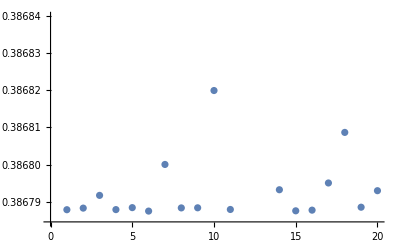

```mathematica
ListPlot[SqueezeTableduration]
```

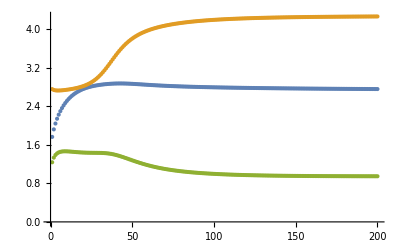

```mathematica
ListPlot[Transpose[ϕTable]]
```

```mathematica
MinSqueeze=Table[0,{i,1,durationnumber}];
Minphi=Table[0,{i,1,durationnumber}];
Do[
MinSqueeze[[i]]=Min[SqueezeTableduration[[i]]];
Minphi[[i]]=phiMinTableduration[[i,Flatten[Position[SqueezeTableduration[[i]],Min[SqueezeTableduration[[i]]]]][[1]]]];
,{i,1,durationnumber}]
```

```mathematica
phiMinTableduration
```

{{{2.90747,1.57091,0.23293},{2.90634,1.57092,0.233901},{0.242581,1.57533,2.92084},{2.90816,1.57075,0.233935},{2.91643,1.57046,0.228415},{2.90919,1.57083,0.232048},{0.213613,1.56306,2.89077},{2.90631,1.5709,0.234148},{0.237416,1.57262,2.91292},{0.261138,1.58325,2.94046},{2.90881,1.57064,0.234461},{0.182525,1.55205,2.86823},{0.269557,1.58738,2.95216},{0.219832,1.56558,2.89666},{2.9088,1.5711,0.229709},{2.90828,1.57081,0.233198},{0.218731,1.56486,2.89434},{0.255982,1.58085,2.93404},{0.228704,1.56888,2.90367},{2.75738,4.26434,0.947275}}}

```mathematica
2.9091890552946875,1.5708308510545996,0.23204820931369552
```

```mathematica
SqueezeTableduration
```

{{0.386788,0.386788,0.386792,0.386788,0.386788,0.386787,0.3868,0.386788,0.386788,0.38682,0.386788,0.386862,0.386845,0.386793,0.386788,0.386788,0.386795,0.386809,0.386789,0.386793}}

```mathematica
MinSqueeze
```

{0.386787}

```mathematica
0.38756199044614875*1.5
```

0.581343

```mathematica
Minphi
```

{{3.24133,1.57174,-0.102178}}

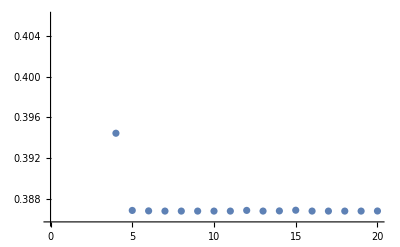

```mathematica
ListPlot[MinSqueeze]
```